Universidad de Jaén. EPS Jaén.
Departamento de Matemáticas. Grado en Ingeniería Informática
Análisis y Métodos Numéricos. 
F. Javier Muñoz Delgado

## Problemas de examen resueltos. Tema 1. Números reales

## Problemas de ecuaciones con valor absoluto

## 1.- Resolver ||x-1|-1|=1 Enero 18

Solución:
Si el valor absoluto de una expresión vale a, entonces la expresión puede tomar dos valores, a ó -a. Sabiendo esto obtenemos:
	 ||x-1|-1|=1 ⟹ |x-1|-1=1 ó  |x-1|-1=-1 
En el primer caso, 	 |x-1|-1=1 ⟹ |x-1|= 2 ⟹ x-1= 2 ó -2 ⟹ x =3 ó -1
En el segundo caso,  |x-1|-1=-1 ⟹ |x-1|= 0 ⟹ x-1= 0 ⟹ x= 1

Hay 3 soluciones: -1, 1 y 3.
Con el Mathematica,

```mathematica
Reduce[Abs[Abs[x-1]-1]==1,x,Reals]
```

x==-1||x==1||x==3

## 1.- Resolver ||x-1|-2|=3. Enero 21

Solución:
Si el valor absoluto de una expresión vale a, entonces la expresión puede tomar dos valores a o -a. Sabiendo esto, 
	||x-1|-2|=3 ⟹ |x-1| - 2 = ±3 
En el primer caso, 	 |x-1| - 2 = 3   ⟹|x-1| =5  (de nuevo tenemos dos posibilidades) ⟹  x-1=5 ó x-1=-5 ⟹ x=6 ó x=-4.
En el segundo caso,  |x-1| - 2=-3  ⟹|x-1| =-1 (como ningún valor absoluto puede ser negativo, no hay solución en este caso)

Agrupando las conclusiones de ambos casos, las soluciones de la ecuación son x=6 y x=-4.

Con el Mathematica,

```mathematica
Reduce[Abs[Abs[x-1]-2]==3,x,Reals]
```

x==-4||x==6

## 1.- Resolver |x^2+2x| = 1 Enero 20

Solución: 
Si el valor absoluto de una expresión vale a, entonces la expresión es a o -a. Sabiendo esto, 
	x^2+2x=1 ó x^2+2x=-1. 
Por tanto, 
		x^2+2x-1=0, es decir,  x = (-2 ± Sqrt[4 + 4])/2  . Por tanto, x=-1-√2, x=-1+√2, 
ó 
		x^2+2x+1=0, es decir, x=(-2 ± Sqrt[4 -4])/2 = -1. 

En resumen, hay tres soluciones: x= -1-√2, -1+√2, - 1.

Con el Mathematica,

```mathematica
Reduce[Abs[x^2+2x]==1,x,Reals]
```

x==-1||x==-1-√2||x==-1+√2

## 1.- Resolver |(x+1)/(x-1)|=2 Enero 2019

Solución:
Si el valor absoluto es dos, la expresión debe ser igual a -2 o a 2. 
|(x+1)/(x-1)|=2 ⟹ (x+1)/(x-1) = -2 ó (x+1)/(x-1) = 2 ⟹(Estudiamos cada igualdad)⟹ 
	 x+1 = -2(x-1) ⟹  x+1 = -2x+2 ⟹  3x= 1 ⟹  x= 1/3
 ó
  	x+1 = 2(x-1 ) ⟹  x+1 = 2x-2  ⟹   3 = x.
  
Las soluciones de la ecuación son x=1/3 y x=3.
Con el Mathematica,

```mathematica
Reduce[Abs[(x+1)/(x-1)]==2,x,Reals]
```

x==1/3||x==3

## 1.- Resolver |(x^2-3x+4)/(x-1)| = 2. Julio 21

Solución:
Si el valor absoluto de una expresión vale a, entonces la expresión es a ó -a. Sabiendo esto, 
	|(x^2-3x+4)/(x-1)| = 2 ⟹ (x^2-3x+4)/(x-1) = ± 2 
Estudiamos cada caso:
	(x^2-3x+4)/(x-1) =  2 ⟹ x^2-3x+4 = 2(x-1)= 2x-2 ⟹ x^2-5x+6 = 0 ⟹ x= 2 ó 3. 
ó
	(x^2-3x+4)/(x-1) =  -2 ⟹ x^2-3x+4 = -2(x-1)= -2x+2 ⟹ x^2-x+2 = 0 ⟹ No hay soluciones reales de esta ecuación, son complejas

Por tanto, las soluciones de la ecuación son x=2 y x=-3.

Con el Mathematica,

```mathematica
Reduce[Abs[(x^2-3x+4)/(x-1)]==2,x,Reals]
```

x==2||x==3

## Problemas de inecuaciones con valor absoluto

## 1.- Resolver ||x-1|-1|<1 Octubre 2021

Solución:
Si el valor absoluto de una expresión vale menos de un número positivo a, entonces la expresión está entre -a y a. Sabiendo esto obtenemos:
	 ||x-1|-1|<1 ⟹ -1<|x-1|-1<1 ⟹(sumando 1 en cada término) ⟹ 0<|x-1|< 2 
Es decir, deben cumplirse las dos condiciones:
	0<|x-1|
	|x-1|< 2 
La primera desigualdad significa que x es distinto de 1, x ≠1,  y la segunda que  -2<x-1<2 .

En resumen,  x ≠1  y -1< x <3.

Por tanto, las soluciones son los números de los intervalos (-1,1) y (1,3).

Con el Mathematica

```mathematica
Reduce[Abs[Abs[x-1]-1]<1,x,Reals]
```

-1<x<1||1<x<3

## 1.- Resolver ||3-2x|-1|≤4. Enero 22

Solución:
Si el valor absoluto de una expresión es menor o igual a 4, entonces la expresión debe estar entre -4 y 4. Sabiendo esto, 
||3-2x|-1|≤4 ⟹ -4 ≤ |3-2x|-1≤4   (sumando 1 en cada término) ⟹  -3 ≤ |3-2x|≤5. 

Es decir, deben cumplirse las dos condiciones:
	-3 ≤ |3-2x|
	|3-2x|≤5
Dado que un valor absoluto no puede ser negativo, tenemos que siempre se cumplirá la primera desigualdad. Por tanto, estudiamos la segunda.   
	|3-2x|≤5 
De nuevo si un valor absoluto es menor o igual que 5, la expresión debe estar ente -5 y 5. 
	|3-2x|≤5 ⟹ -5 ≤ 3-2x ≤ 5  (restando 3 en cada término) ⟹ -8 ≤ -2x ≤ 2  (dividiendo entre -2) ⟹ 4 ≥ x ≥ -1 (al multiplicar o dividir por un negativo, las desigualdades cambian) ⟹ -1 ≤ x ≤ 4.

Por tanto, las soluciones de la inecuación son los valores comprendidos entre el -1 y el 4 (ambos incluidos).
Con el Mathematica sería:

```mathematica
Reduce[Abs[Abs[3-2x]-1]<= 4, x ,Reals]
```

-1≤x≤4

## 2.- Resolver ||3-3x|-3|<3. Julio 2024

Solución:
En general, si  |x|< a  ⟹ -a < x < a. Por tanto, si ||3-3x|-3|< 3  ⟹-3<|3-3x|-3<3 
Sumando 3 en cada término:
	 0<|3-3x|<6.
Es decir, deben cumplirse las dos condiciones:
	 |3-3x|<6.
	 0<|3-3x|.
Por tanto, 
|3-3x|<6 ⟹-6 < 3-3x <  6 ⟹-9 < -3x <  3 ⟹ 3 > x > -1   
3-3x≠0 ⟹ 3 ≠ 3x ⟹ 1 ≠ x
Para que se cumplan las dos condiciones x debe estar en (-1,1) ∪ (1,3). 

Con el Mathematica sería:

```mathematica
Reduce[Abs[Abs[3-3x]-3]<3,x,Reals]
```

-1<x<1||1<x<3

## 1.- Resolver |(x+1)/(x-1)|≤4. Enero 2023

Solución:
Si el valor absoluto de una expresión es menor o igual a 4, entonces la expresión debe estar entre -4 y 4. Sabiendo esto, 
	|(x+1)/(x-1)|≤4 ⟹ -4 ≤ (x+1)/(x-1) ≤4  . 

Para multiplicar por x-1 y despejar necesitamos distinguir los casos x-1>0 y x-1<0
Caso 1: x-1>0 (es decir, x>1) Al multiplicar por una cantidad positiva, la desigualdad no cambia.
	-4 (x-1) ≤ x+1  ≤ 4 (x-1) .  Por tanto, - 4x + 4 ≤ x+1  ≤ 4x - 4 .
		La primera desigualdad,  - 4x + 4 ≤ x+1 , se cumple cuando  3 ≤ 5x, es decir 3/5 ≤ x. Lo que es obvio, pues estamos en el supuesto x >1.
		La segunda desigualdad, x + 1 ≤ 4x -4 , se cumple cuando  5 ≤ 3x, es decir 5/3 ≤ x. Es necesario que x sea mayor o igual que 5/3.
Caso 2: x-1<0 (es decir, x<1) Al multiplicar por una cantidad negativa, la desigualdad cambia.
	-4 (x-1) ≥ x+1  ≥ 4 (x-1) .  Por tanto, - 4x + 4 ≥ x+1  ≥ 4x - 4 .
		La primera desigualdad,  - 4x + 4 ≥ x+1 , se cumple cuando  3 ≥ 5x, es decir 3/5 ≥ x. Es necesario que x sea menor o igual que 3/5.
		La segunda desigualdad, x + 1 ≥ 4x -4 , se cumple cuando  5 ≥ 3x, es decir 5/3 ≥ x. Lo que es obvio, pues estamos en el supuesto x <1.

Resumiendo, para el caso x>1, es necesario que x≥5/3, y para el caso x<1, es necesario que x≤3/5.

Las soluciones de la inecuación son los números del conjunto (-∞, 3/5] ∪ [5/3, ∞)

Con el Mathematica sería:

```mathematica
Reduce[Abs[(x+1)/(x-1)]<= 4, x ,Reals]
```

x≤3/5||x≥5/3

## Problemas de inducción

## 1.- Demostrar, usando inducción, que 1*2 + 2*3 + 3*4 + ...+ n(n+1) = (n(n+1)(n+2))/3 para n = 1, 2, 3, 4, ... Julio-Octubre 18

Solución:
Para realizar la demostración por inducción, comenzamos estudiando el primer caso, n=1. 
El primer término, que empieza con 1*2, debe terminar cuando n=1 con 1*(1+1), por tanto se reduce a un sumando. La igualdad que habría que comprobar es:
1*2  = (1(1+1)(1+2))/3. Es inmediato comprobar que ambas expresiones valen 2.
En la segunda parte del método de inducción, se supone que la propiedad es cierta para un valor n y se trata de comprobar que también lo es para (n+1).

Es decir, si la igualdad es cierta para n, 1*2 + 2*3 + 3*4 + ...+ n(n+1) = (n(n+1)(n+2))/3, se trataría de demostrar que también lo será para (n+1).

El primer termino de la expresión para (n+1) es:
1*2 + 2*3 + 3*4 + ...+ n(n+1)+ (n+1)(n+1+1) =1*2 + 2*3 + 3*4 + ...+ n(n+1)+ (n+1)(n+2) 

El segundo término de la expresión para n+1 es
 ((n+1)((n+1)+1)((n+1)+2))/3 = ((n+1)(n+2)(n+3))/3
Tenemos que demostrar que si es cierto para n, también lo es para n+1, es decir que si  1*2 + 2*3 + 3*4 + ...+ n(n+1) = (n(n+1)(n+2))/3 también será cierto que
	1*2 + 2*3 + 3*4 + ...+ n(n+1)+ (n+1)(n+2) =((n+1)(n+2)(n+3))/3
Observamos que los primeros sumandos de la primera expresión son los de la expresión para n, por tanto,
 1*2 + 2*3 + 3*4 + ...+ n(n+1)+ (n+1)(n+2) =(n(n+1)(n+2))/3 + (n+1)(n+2) = (n+1)(n+2)(n/3+1) =(n+1)(n+2)((n+3)/3) = ((n+1)(n+2)(n+3))/3
 y concluimos que de ser cierta la igualdad para n, también lo es para (n+1).

## 1.- Demostrar por inducción que 1*4+2*5+3*6+...+n(n+3) =n(1+n)(5+n)/3, para todo número natural (n= 1, 2, 3, ...). Julio 2024

Solución:
Para realizar la demostración por inducción realizamos los dos pasos:
1) Comprobar que la propiedad es cierta para el primer valor, n=1.
		1*4=4
		1(1+1)(5+1)/3=4
		Son iguales.
2) Suponiendo que la propiedad se cumple hasta cierto valor de n, comprobemos que también es cierto para n+1:
	Es decir, que suponiendo que 1*4+2*5+3*6+...+n(n+3) =n(1+n)(5+n)/3, debemos ver que también sea cierto 
	1*4+2*5+3*6+...+n(n+3)+(n+1)(n+1+3) =(n+1)(1+(n+1))(5+(n+1))/3.
	Es decir, debemos ver si
	1*4+2*5+3*6+...+n(n+3)+(n+1)(n+4) =(n+1)(n+2)(n+6)/3
	Para ello partimos de esta segunda expresión, y como nos encontramos en el primer miembro de la segunda al primer miembro de la primera igualdad, la sustituimos:
	1*4+2*5+3*6+...+n(n+3)+(n+1)(n+4)= n(1+n)(5+n)/3 + (n+1)(n+4)
Ahora tendríamos que ver si son iguales
	n(1+n)(5+n)/3 + (n+1)(n+4) = (n+1)(n+2)(n+6)/3
Simplificamos (n+1)
	n(5+n)/3 + (n+4) = (n+2)(n+6)/3
Multiplicando por 3
	n(5+n) + 3(n+4) = (n+2)(n+6)
Desarrollando cada término
	5n+n^2+3n+12 = n^2+6n+2n+12
Por tanto,
	n^2+8n+12 = n^2+8n+12
Tenemos que las dos expresiones son iguales.

Por tanto, la propiedad es cierta para todos los números naturales.

## 4.- Demostrar por inducción que n^3+2n es múltiplo de 3 para n=1, 2, 3,... Enero 2023

Solución:
En el método de inducción hay que realizar dos pasos:
	1) Comenzamos viendo que es cierto para el primer valor, n=1. 
		1^3+2*1=3, es múltiplo de 3.
	2) Supongamos ahora que es cierto hasta un valor k, y veamos si es cierto para k+1.
		Suponiendo que k^3+2k  es múltiplo de 3, veamos si (k+1)^3+2(k+1) también lo es. Haciendo cálculos en esta última expresión:
	 		(k+1)^3+2(k+1) = k^3+3 k^2+3k+1 + 2k+2 = k^3+2k +3 k^2+3k+3  =  (k^3+2k) +3(k^2+k+1) 
	(Hay que tratar de que aparezca la expresión para k, en la expresión de k+1, para usar la hipótesis de inducción) 

		Es múltiplo de 3, pues el primer sumando es múltiplo de 3, por la suposición en la inducción, y el segundo es obviamente también múltiplo de 3.

## 1. - Demostrar por inducción que 4n^3 + 8n + 12 es múltiplo de 12 para n=1, 2, 3, ... Octubre 2022

Solución:
Para realizar la demostración por inducción, empezamos comprobando si la propiedad es cierta para el primer caso, n=1. 
Efectivamente, 4*1^3 + 8*1 + 12=24 es múltiplo de 12.
Ahora, suponiendo que sea cierto hasta un número n, debemos demostrar que también lo será para el siguiente número, n+1.
Así suponemos que 4n^3 + 8n + 12 es múltiplo de 12, y tratamos de demostrar que también lo es: 4(n+1)^3 + 8(n+1) + 12 . Operamos en esta última expresión y buscamos que aparezca la anterior:
4(n+1)^3 + 8(n+1) + 12 =4(n^3+3 n^2+3n+1) + 8n + 8 + 12 = 4n^3+12 n^2+12n+4 + 8n + 8 + 12 = 4n^3+8n + 12 +12 n^2+12n+4+8 = 4n^3+8n + 12 +12(n^2+n+1).

Por tanto, suponiendo que 4n^3 + 8n + 12 es múltiplo de 12, también lo es la expresión para n+1.

## 4.- Demostrar que todo número impar (1, 3, 5, 7, 9, ...) al cuadrado es un múltiplo de 8 más 1. Julio 2023

Solución:
Una opción es escribir los números impares de la forma (2n-1) con n cualquier número natural, n=1, 2, 3, 4, .... Su cuadrado será 
(2n-1)^2= 4 n^2-4n+1 = 4(n^2-n)+1= 4n(n-1)+1.
Como alguno de los números n ó (n-1) tiene que ser par, n(n-1) será múltiplo de dos y, por tanto, 4n(n-1) será múltiplo de 8.

Si optamos por el método de inducción hay que realizar dos pasos:
	1) Comenzamos viendo que es cierto para el primer valor, n=1. 
		1^2=1, es 1 más 0 (este último, el 0, es múltiplo de 8).
	2) Supongamos ahora que es cierto hasta n=k, es decir para el impar 2k-1, y veamos si es cierto para k+1:
		Es decir, que suponiendo que (2k-1)^2 = 4k^2-4k+1 es múltiplo de 8 más 1, veamos si (2(k+1)-1)^2 también lo es. Haciendo cálculos en esta última expresión, tratamos de encontrar la expresión 4k^2-4k+1:
	 		(2(k+1)-1)^2 = (2k+2-1)^2 =(2k+1)^2=4 k^2+4k+1= (4k^2-4k+1) + 8k
Como el primer sumando es múltiplo de 8 más 1, al sumarle 8k también será múltiplo de 8 más 1.

## 1.- Demostrar por inducción que 3^(2n)-1 es múltiplo de 8 para n=1, 2, 3, ... Julio 22

Solución:
Para realizar la demostración por inducción, empezamos comprobando si la propiedad es cierta para el primer caso, n=1. 
Efectivamente, 3^(2*1)-1=9-1=8 es múltiplo de 8.
Ahora, suponiendo que sea cierto hasta un número n, debemos demostrar que también lo será para el siguiente número, n+1.
Así suponemos que 3^(2n)-1 es múltiplo de 8, y tratamos de demostrar que también lo es: 3^(2(n+1))-1 .

3^(2(n+1))-1= 3^(2n+2)-1 = 3^2 3^(2n)-1  =9* 3^(2n)-1 =9*(3^(2n)-1)+ 9 - 1 = 9*(3^(2n)-1) + 8  (es nueve veces un múltiplo de 8 más 8). Por tanto, suponiendo que 3^(2n)-1 es múltiplo de 8, también lo es la expresión para n+1.

## 1.- Supongamos que queremos calcular la suma de n términos, por ejemplo la suma de los n primeros números impares; 1 + 3 + 5 + 7 + ... + (2n-1) y que conjeturamos que la suma debe ser una expresión polinómica en n, en este caso, de segundo grado, p(n). Calculando la suma para n=1, n=2 y n=3, obtener el polinomio p(n) de ℙ_2 que interpola esos valores. Obtenido p(n), demostrar por inducción que 1+3+5+7+...+(2n-1) es p(n), para todo número natural n. Enero 2024

Solución: 
Siguiendo lo indicado en el problema, empezamos por calcular el polinomio de segundo grado p(n) que interpola la suma de los impares para n=1, n=2 y n=3.
		p(1)=1
		p(2)=1+3=4
		p(3)=1+3+5=9
Para calcular el polinomio de grado dos que toma estos valores, puede hacerse de varias formas. Si utilizamos la idea de Newton, el polinomio podemos escribirlo en la forma p(n)=A+B(n-1)+C(n-1)(n-2). Ahora podemos evaluar el polinomio en los tres puntos e igualamos a los valores. 
p(1) = A+B(1-1)+C(1-1)(1-2) = 1 ⟹ A = 1
p(2) = A+B(2-1)+C(2-1)(2-2) = 4 ⟹ A + B = 4 ⟹ 1 + B = 4 ⟹ B = 3
p(3) = A+B(3-1)+C(3-1)(3-2) = 9 ⟹ A + 2B + 2C = 9 ⟹ 1 + 2*3 + 2C = 9 ⟹ 2C = 2 ⟹ C=1
Por tanto, p(n) = 1 + 3(n-1) + (n-1)(n-2) = 1 + 3n -3 + n^2 -3n + 2 = n^2

En la segunda parte del problema, hay que demostrar por inducción que 1+3+5+7+...+(2n-1) es p(n), es decir n^2, para todo número natural n. Para demostrarlo por inducción, estudiamos los dos pasos:
1) El caso n=1, es cierto que la suma del primer impar es p(1). 
		1 = p(1)=1.
2) Suponemos que es cierto hasta un valor de n,
		1+3+5+7+...+(2n-1) = p(n) = n^2
	Veamos si es cierto para n+1
		1+3+5+7+...+(2n-1)+(2(n+1)-1) = p(n+1) = (n+1)^2
	Utilizando la hipótesis de inducción, el primer sumando quedaría como
	1+3+5+7+...+(2n-1) + (2(n+1)-1) = n^2 + (2(n+1)-1) = n^2 + (2n+2-1) = n^2 + 2n + 1
	El segundo sumando es
		(n+1)^2 =n^2 + 2n + 1
	Por tanto, son iguales y la propiedad sería también cierta para n+1.
Podemos concluir que la propiedad es cierta para todos los números naturales.

## Otros problemas

## 1.- Razonar cuál de los siguientes números es racional y expresarlo como cociente de dos números enteros: 0,010101010101... = ∑_(n=1)^∞ 1/10^(2n) , 0,1001000010000001.... = ∑_(n=1)^∞ 1/(10^(n^2)) . Julio 2023

Comentarios:
Los números racionales son los cocientes de números enteros, a/b, con b>0. Al realizar la división de a entre b, puede obtenerse un número entero, en otro caso, para obtener una forma numérica decimal, “sacamos decimales” y tiene que llegar un momento en que los restos posibles (que serán números entre 0 y b-1) se tienen que repetir de forma indefinida y se origina un periodo. De igual forma, si un número tiene un desarrollo decimal, donde a partir de un momento, una sucesión de cifras se repite sucesivamente y de forma indefinida, podemos expresar el número como cociente de dos enteros. 
Además de los racionales, hay más números, algunos utilizados con mucha frecuencia como la raíz de dos, el número π, el logaritmo de 2, etc. Estos números forman parte de los irracionales, números reales que no son racionales. Estos números no tienen un desarrollo decimal periódico.

Solución:
Observamos que el primer número es periódico. El par de cifras 01 se repite continuamente. Se trata de un número racional. Para ponerlo como fracción escribimos
				x = 0,01010101...   
			100 x = 1,01010101...
Restando de la segunda expresión la primera:  99 x = 1. Por tanto, x=1/99.

El segundo número tiene un desarrollo decimal que no es periódico. Hay dos ceros entre los primeros dos unos, luego hay cuatro ceros, después seis ceros, etc. No es un número racional.
 
Con el Mathematica sería:

```mathematica
Sum[1/10^(2n),{n,1,Infinity}]
```

1/99

```mathematica
Sum[1/10^(n^2),{n,1,Infinity}]
```

1/2 (-1+EllipticTheta[3,0,1/10])

## 5.- Expresar el número 12’345454545... como cociente de dos números enteros. Julio 22

Llamando               x=12’345454545... 
Tenemos que 10 x = 123’45454545... 
También       1000x = 12345’454545...
Restando, 1000x - 10x = 12345-123. Por tanto, 990 x = 12222, x=12222/990.  Si queremos simplificar, que no es necesario, dividimos numerador y denominador por 2 y por 9. 12222/990 = 1358/110 = 679/55.

Otra forma sería escribir el número como una suma con una serie geométrica (y aplicar la fórmula para la suma en este caso).

12’3454545... = 12 +  3/10+ ∑_(n=1)^∞ 45/(10*100^n) = 120/10 +  3/10+45/10 ∑_(n=1)^∞ 1/100^n = 123/10 +45/10 (1/100)/(1-1/100) = 123/10 +45/10 1/(100-1) = 123/10 +45/10 1/99 = 123/10 +45/990 = 123/10 +5/110 = 123/10 +1/22 = (123*22+10)/220 =  2716/220= 2716/220 = 679/55

## 1.- Obtener los valores de x para los que x^2 < |x|. Expresar el conjunto por medio de intervalos, decir si es abierto o cerrado, si está acotado superior o inferiormente, si tiene máximo o mínimo, supremo o ínfimo. Enero 2019

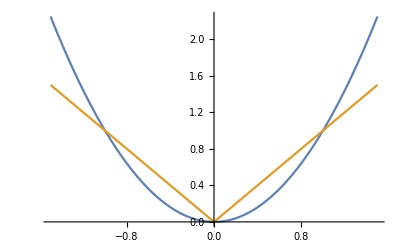
Solución: 	
El valor absoluto de x puede ser x ó -x, según sea x mayor o menor que cero. Distinguimos los dos casos:
	Cuando x es mayor que cero, la desigualdad queda como:  x^2 < |x|=x . Estudiaremos la desigualdad:   x^2 < x . Restando x,   x^2-x<0 ⟹ x(x-1)<0. Como x>0 ⟹ x-1 debe ser menor que 0 ⟹ x<1
	
	Cuando x es menor que cero,  la desigualdad queda como:  x^2 < |x|=-x . Estudiaremos la desigualdad:   x^2 < -x . Sumando x,   x^2+x<0 ⟹ x(x+1)<0. Como x<0 ⟹ x+1 debe ser mayor que 0 ⟹ x>-1
	
En el caso x=0, no se cumple la desigualdad.

Por tanto, cuando x es mayor que cero, debe ser menor que 1 y cuando x es menor que cero, debe ser mayor que -1. Luego el conjunto es (-1,0) ∪ (0,1). 
Se trata de un conjunto abierto, acotado superior e inferiormente, el supremo es 1, el ínfimo es -1, no tiene máximo, ni mínimo.

Si dibujamos las gráficas de las dos funciones:
			-Graphics-
Vemos que el valor absoluto está por encima de la gráfica de x^2 cuando x está en (-1,0) y en (0,1).
 
Con el Mathematica,

```mathematica
Reduce[x^2<Abs[x],x,Reals]
```

-1<x<0||0<x<1

## Problemas para el Aula de Informática (puede utilizarse el Mathematica)

## 1.- Calcular el conjunto de los x que cumplen 6-5 x+x^3<2+x. Decir si es acotado superior o inferiormente, si tiene supremo o ínfimo, máximo o mínimo, indicando sus valores. Enero 2019, Aula de Informática

Solución :

```mathematica
Reduce[6-5x+x^3<2+x,x]
```

x<-1-√3||-1+√3<x<2

El resultado que nos da el Mathematica nos indica que el conjunto solución de esta inecuación es (-∞, -1-√3)U(-1+√3,2).
Es un conjunto acotado superiormente, pero no tiene corta inferior. No tiene máximo, ni mínimo. Tiene supremo que es el 2, pero no pertenece al conjunto, por eso no es el máximo.

## 2.- Estudiar el conjunto de los números reales que cumplen x - |x-1| < 1. Decir si está acotado inferior o superiormente, si tiene supremo o ínfimo. Enero 19, Aula de Informática

```mathematica
Reduce[x-Abs[x-1]<1,x,Reals]
```

x<1

El conjunto de soluciones de la inecuación es (-∞,1). Se trata de un conjunto acotado superiormente, pero no inferiormente. Los números mayores o iguales que 1 son cotas superiores. La menor cota superior, el supremo, es el 1. Al no estar acotado inferiormente, no tiene ínfimo.

## 1.- Calcular el conjunto de los x que cumplen 6-5 x+x^3<2+x. Decir si es acotado superior o inferiormente, si tiene supremo o ínfimo, máximo o mínimo, indicando sus valores. Enero 19, Aula de Informática

Solución: Utilizando el Mathematica

```mathematica
Reduce[6-5x+x^3<2+x,x]
```

x<-1-√3||-1+√3<x<2

De donde deducimos que x tiene que estar en (-∞,-1-√3) ∪ (-1+√3,2). Es un conjunto acotado superiormente, pero no inferiormente. Tiene supremo que sería el 2, pero no tiene ínfimo, ni máximo, ni mínimo.

## 2.- Estudiar el conjunto de los números reales que cumplen x - |x-1| < 1. Decir si está acotado inferior o superiormente, si tiene supremo o ínfimo. Enero 21, Aula de Informática

```mathematica
Reduce[x-Abs[x-1]<1,x,Reals]
```

x<1

El conjunto de soluciones de esta inecuación es (-∞,1). Este conjunto está acotado superiormente, pero no inferiormente. Tiene supremo, el 1, pero no tiene tiene ínfimo.

## 1.- Calcular el conjunto de los x que cumplen 7-6x+x^3≥7-x^2. Decir si es acotado superior o inferiormente, si tiene supremo o ínfimo, máximo o mínimo, indicando sus valores. Enero 20, Aula de informática

```mathematica
Reduce[7-6x+x^3≥ 7-x^2,x,Reals]
```

-3≤x≤0||x≥2

Solución:
Conjunto Solución:   [-3,0] ∪ [2,∞)                            
Acotado superior:  NO                             Acotado Inferior: SI
Máximo:        NO            Mínimo:      -3           Supremo:      NO                Ínfimo: -3

## 2.- Dado el conjunto de los números reales x que cumplen 2-5 x+x^3≥2+x, escoger la respuesta correcta: 1) Está acotado superiormente, 2) Tiene supremo, 3) Contiene al [2,3], 4) Tiene mínimo, 5) Tiene máximo Julio 2022, Aula de informática

```mathematica
Reduce[2-5x+x^3>=2+x,x]
```

-√6≤x≤0||x≥√6

El conjunto de soluciones de la inecuación es [-√6,0] ∪ [√6,∞). El mínimo es -√6, no tiene máximo, ni está acotado superiormente, ni tiene supremo.

## 3.- El conjunto de las soluciones de la ecuación 2 < x^2/((x-3)(x+3)) ≤ 4. 1) No está acotado superiormente , 2) Tiene máximo absoluto, 3) Tiene cota inferior, 4) Tiene mínimo, 5) No tiene soluciones 1) Está acotado superiormente, 2) No tiene máximo absoluto, 3) No tiene cota superior, 4) Tiene mínimo, 5) No tiene soluciones 1) No está acotado superiormente, 2) Tiene máximo absoluto, 3) Tiene cota superior, 4) Tiene mínimo, 5) No tiene soluciones 1) Está acotado superiormente 2) Tiene máximo absoluto, 3) No tiene cota inferior, 4) Tiene mínimo, 5) No tiene soluciones Julio 2023. Aula de informática

```mathematica
Reduce[2<x^2/((x-3)(x+3))<= 4,x]
```

-3 √2<x≤-2 √3||2 √3≤x<3 √2

El conjunto de soluciones de la ecuación es: (-3 √2,-2 √3]∪[2 √(3,)3 √2). Por tanto, está acotado superior e inferiormente, tiene cotas superiores e inferiores, está acotado, no tiene máximo, ni mínimo.

## 3.- El conjunto de las soluciones de la ecuación |(x+1)/(x-1)|≤4. 1) Está acotado superiormente 2) Tiene máximo absoluto, 3) Tiene cota inferior, 4) No tiene mínimo, 5) No tiene soluciones Enero 2023. Aula de informática

```mathematica
Clear["Global`*"]
```

```mathematica
Reduce[Abs[(x+1)/(x-1)]<=4,x,Reals]
```

x≤3/5||x≥5/3

El resultado que nos da el Mathematica nos indica que el conjunto solución de esta inecuación es (-∞, 3/5]U[5/3,∞).
El conjunto de soluciones no está acotado inferior, ni superiormente, no tiene máximo, ni mínimo.

## 3.- El conjunto de las soluciones de la ecuación |(x-1)/(x+1)|<4. 1) Está acotado superiormente 2) Tiene máximo absoluto, 3) No tiene cota inferior, 4) Tiene mínimo, 5) No tiene soluciones Enero 2023. Aula de informática

```mathematica
Clear["Global`*"]
```

```mathematica
Reduce[Abs[(x-1)/(x+1)]<4,x,Reals]
```

x<-5/3||x>-3/5

El resultado que nos da el Mathematica nos indica que el conjunto solución de esta inecuación es (-∞, -5/3)U(-3/5,∞).
La inecuación tiene soluciones. El conjunto de soluciones no está acotado inferior, ni superiormente, no tiene máximo, ni mínimo.

## 3.- El conjunto de las soluciones de la ecuación |(x+1)/(x-1)|< 4. 1) Está acotado superiormente 2) Tiene máximo absoluto, 3) Tiene cota inferior, 4) No tiene mínimo, 5) No tiene soluciones Enero 2023. Aula de informática

```mathematica
Clear["Global`*"]
```

```mathematica
Reduce[Abs[(x+1)/(x-1)]<4,x,Reals]
```

x<3/5||x>5/3

El resultado que nos da el Mathematica nos indica que el conjunto solución de esta inecuación es (-∞, 3/5)U(5/3,∞).
La inecuación tiene soluciones. El conjunto de soluciones no está acotado inferior, ni superiormente, no tiene máximo, ni mínimo.

## 3.- El conjunto de las soluciones de la ecuación |(x-1)/(x+1)|>4. 1) No tiene cota inferior, 2) Tiene mínimo, 3) No tiene soluciones, 4) Está acotado inferiormente, 5) Tiene máximo absoluto Enero 2023. Aula de informática

```mathematica
Clear["Global`*"]
```

```mathematica
Reduce[Abs[(x-1)/(x+1)]>4,x,Reals]
```

-5/3<x<-1||-1<x<-3/5

El resultado que nos da el Mathematica nos indica que el conjunto solución de esta inecuación es (-5/3, -1)U(-1,-3/5).
La inecuación tiene soluciones. El conjunto de soluciones está acotado inferior y superiormente, no tiene máximo, ni mínimo.